```mathematica
Zx = R1 +ZC1*( ZC1 + R2*R3/(R2+R3)/(2*ZC1 + R2*R3/(R2+R3)))
```

R1+ZC1 (ZC1+(R2 R3)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1)))

```mathematica
Simplify[Zx]
```

R1+ZC1 (ZC1+(R2 R3)/(R2 R3+2 R2 ZC1+2 R3 ZC1))

```mathematica
Ix = Ux/Zx
```

Ux/(R1+ZC1 (ZC1+(R2 R3)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1))))

```mathematica
IXC1 = Ix*ZC1/(2*ZC1 + R2*R3/(R2+R3))
```

(Ux ZC1)/(((R2 R3)/(R2+R3)+2 ZC1) (R1+ZC1 (ZC1+(R2 R3)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1)))))

```mathematica
Uy = IXC1*R2*R3/(R2+R3)
```

(R2 R3 Ux ZC1)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1) (R1+ZC1 (ZC1+(R2 R3)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1)))))

```mathematica
Gu = Uy/Ux
```

(R2 R3 ZC1)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1) (R1+ZC1 (ZC1+(R2 R3)/((R2+R3) ((R2 R3)/(R2+R3)+2 ZC1)))))

```mathematica
Simplify[Gu]
```

(R2 R3 ZC1)/(2 R1 R3 ZC1+2 R3 ZC1^3+R1 R2 (R3+2 ZC1)+R2 ZC1 (R3+R3 ZC1+2 ZC1^2))

```mathematica
C1 = 166.667*10^-9;
R1 = 8; R2 = 16; R3 = 24;
```

```mathematica
1/((C1^2)*R1*R2*R3/(R2+R3))
```

4.68748×10^11

```mathematica
(2R1 + R2*R3/(R2+R3))/(C1*R1*R2*R3/(R2+R3))
```

2.×10^6

```mathematica
Gu = AbsArg[((1/C1*R1)*I*w)/(((I*w)^2+(2R1+R2*R3/(R2+R3))/(C1*R1*R2*R3/(R2+R3)))*I*w)+1/(C1^2*R1*R2*R3/(R2+R3))]
```

{Abs[4.68748×10^11+(4.79999×10^7+0. ⅈ)/(2.×10^6-w^2)],Arg[4.68748×10^11+(4.79999×10^7+0. ⅈ)/(2.×10^6-w^2)]}

```mathematica
Ggg= AbsArg[((1/C1*R1)*I*w)/(((I*w)^2+(2R1+R2*R3/(R2+R3))/(C1*R1*R2*R3/(R2+R3)))*I*w)+1/(C1^2*R1*R2*R3/(R2+R3))][[1]]
```

Abs[4.68748×10^11+(4.79999×10^7+0. ⅈ)/(2.×10^6-w^2)]

```mathematica
Fi = AbsArg[((1/C1*R1)*I*w)/(((I*w)^2+(2R1+R2*R3/(R2+R3))/(C1*R1*R2*R3/(R2+R3)))*I*w)+1/(C1^2*R1*R2*R3/(R2+R3))][[2]]
```

Arg[4.68748×10^11+(4.79999×10^7+0. ⅈ)/(2.×10^6-w^2)]

```mathematica
w0 = 684652;
```

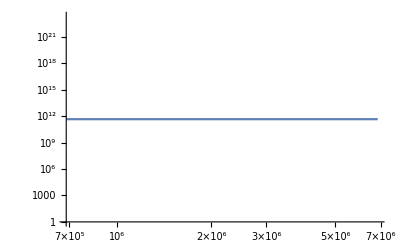

```mathematica
LogLogPlot[Ggg, {w,w0, 10*w0}]
```

```mathematica
LogLinearPlot[Fi, {w, w0, 10*w}]
```

```mathematica
((1/C1*R1)*I*w)/(((I*w)^2+(2R1+R2*R3/(R2+R3))/(C1*R1*R2*R3/(R2+R3)))*I*w)+1/(C1^2*R1*R2*R3/(R2+R3))
```